```mathematica
Needs["Notation`"]
```

```mathematica
Notation[Subscript[V, pdσ] ⟺ pds]
Notation[Subscript[V, pdπ] ⟺ pdpi]
```

```mathematica
(*** we write out the hopping integral of p and d orbitals**)
```

```mathematica
(* pxdxy *)
```

```mathematica
pxdxy = √3 l^2 m pds+ m(1-2l^2) pdpi
```

(1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ

```mathematica
pxdyz=√3 l m n pds - 2 l m n pdpi
pxdzx=√3 l^2 n pds + n(1-2l^2)pdpi
```

-2 l m n V_pdπ+√3 l m n V_pdσ

(1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ

```mathematica
pxdx2=(√3)/2 l(l^2-m^2)pds + l(1-l^2+m^2) pdpi
pxdz2=l(n^2-1/2(l^2+m^2))pds-√3 l n^2 pdpi
```

l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ

-√3 l n^2 V_pdπ+l (1/2 (-l^2-m^2)+n^2) V_pdσ

```mathematica
(***** cyclically permutation : xyz->yzx, lmn->mnl****)
```

```mathematica
pydyz=√3 m^2 n pds+ n(1-2m^2) pdpi
pydzx=√3 l m n pds - 2 l m n pdpi
pydxy=√3 m^2 l pds + l(1-2m^2)pdpi
pydx2=(√3)/2 m(l^2-m^2) pds -m (1+l^2-m^2)pdpi
pydz2=m(n^2-1/2(l^2+m^2))pds-√3 m n^2 pdpi
```

(1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ

-2 l m n V_pdπ+√3 l m n V_pdσ

l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ

-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ

-√3 m n^2 V_pdπ+m (1/2 (-l^2-m^2)+n^2) V_pdσ

```mathematica
(***** cyclically permutation : xyz->yzx, lmn->mnl, second :xyz->yzx->zxy, lmn->mnl->nlm ****)
```

```mathematica
pzdzx = √3 n^2 l pds+ l(1-2n^2) pdpi
pzdxy=√3 l m n pds - 2 l m n pdpi
pzdyz=√3 n^2 m pds + m(1-2n^2)pdpi
pzdx2=(√3)/2 n (l^2-m^2) pds - n(l^2-m^2) pdpi
pzdz2=n(n^2-1/2(l^2+m^2))pds+ √3 n(l^2+m^2) pdpi
```

l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ

-2 l m n V_pdπ+√3 l m n V_pdσ

m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ

-(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ

√3 (l^2+m^2) n V_pdπ+n (1/2 (-l^2-m^2)+n^2) V_pdσ

```mathematica
pdtable=Table[0,{i,1,4},{j,1,6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
pdtable[[2,2]]=pxdxy;
pdtable[[2,3]]=pxdyz;
pdtable[[2,4]]=pxdzx;
pdtable[[2,5]]=pxdx2;
pdtable[[2,6]]=pxdz2;
```

```mathematica
pdtable[[3,2]]=pydxy;
pdtable[[3,3]]=pydyz;
pdtable[[3,4]]=pydzx;
pdtable[[3,5]]=pydx2;
pdtable[[3,6]]=pydz2;
```

```mathematica
pdtable[[4,2]]=pzdxy;
pdtable[[4,3]]=pzdyz;
pdtable[[4,4]]=pzdzx;
pdtable[[4,5]]=pzdx2;
pdtable[[4,6]]=pzdz2;
```

```mathematica
pdtable[[1,2]]= "dxy";
pdtable[[1,3]]= "dyz";
pdtable[[1,4]]= "dzx";
pdtable[[1,5]]= "dx2";
pdtable[[1,6]]= "dz2";
pdtable[[1,1]]="t";
pdtable[[2,1]]="px";
pdtable[[3,1]]="py";
pdtable[[4,1]]="pz";
```

```mathematica
pdtable
```

{{t,dxy,dyz,dzx,dx2,dz2},{px,(1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,(1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ,l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ,-√3 l n^2 V_pdπ+l (1/2 (-l^2-m^2)+n^2) V_pdσ},{py,l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ,(1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ,-√3 m n^2 V_pdπ+m (1/2 (-l^2-m^2)+n^2) V_pdσ},{pz,-2 l m n V_pdπ+√3 l m n V_pdσ,m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ,l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ,-(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ,√3 (l^2+m^2) n V_pdπ+n (1/2 (-l^2-m^2)+n^2) V_pdσ}}

```mathematica
TableForm[pdtable]
```

t | dxy | dyz | dzx | dx2 | dz2
px | (1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ | -2 l m n V_pdπ+√3 l m n V_pdσ | (1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ | l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ | -√3 l n^2 V_pdπ+l (1/2 (-l^2-m^2)+n^2) V_pdσ
py | l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ | (1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ | -2 l m n V_pdπ+√3 l m n V_pdσ | -m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ | -√3 m n^2 V_pdπ+m (1/2 (-l^2-m^2)+n^2) V_pdσ
pz | -2 l m n V_pdπ+√3 l m n V_pdσ | m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ | l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ | -(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ | √3 (l^2+m^2) n V_pdπ+n (1/2 (-l^2-m^2)+n^2) V_pdσ

```mathematica
(*******For 180 configuration left configuration *****)
```

```mathematica
td1={l->-1,m->0,n->0}
```

{l→-1,m→0,n→0}

```mathematica
pdtableleft=pdtable/.td1
```

{{t,dxy,dyz,dzx,dx2,dz2},{px,0,0,0,-1/2 √3 V_pdσ,V_pdσ/2},{py,-V_pdπ,0,0,0,0},{pz,0,0,-V_pdπ,0,0}}

```mathematica
TableForm[pdtableleft]
```

t | dxy | dyz | dzx | dx2 | dz2
px | 0 | 0 | 0 | -1/2 √3 V_pdσ | V_pdσ/2
py | -V_pdπ | 0 | 0 | 0 | 0
pz | 0 | 0 | -V_pdπ | 0 | 0

```mathematica
Grid[{{0,"dxy","dyz","dzx","dx2","dz2"},{"px",0,0,0,-(√3 pds)/2,pds/2},{"py",-pdpi,0,0,0,0},{"pz",0,0,-pdpi,0,0}}]
```

0 | dxy | dyz | dzx | dx2 | dz2
px | 0 | 0 | 0 | -1/2 √3 V_pdσ | V_pdσ/2
py | -V_pdπ | 0 | 0 | 0 | 0
pz | 0 | 0 | -V_pdπ | 0 | 0

```mathematica
Insert[Grid[{{0,"dxy","dyz","dzx","dx2","dz2"},{"px",0,0,0,-(√3 pds)/2,pds/2},{"py",-pdpi,0,0,0,0},{"pz",0,0,-pdpi,0,0}}],{Dividers->All,Spacings->1.5 {1,1}},2]
```

0 | dxy | dyz | dzx | dx2 | dz2
px | 0 | 0 | 0 | -1/2 √3 V_pdσ | V_pdσ/2
py | -V_pdπ | 0 | 0 | 0 | 0
pz | 0 | 0 | -V_pdπ | 0 | 0

```mathematica
td2={l->1,m->0,n->0}
```

{l→1,m→0,n→0}

```mathematica
pdtableright=pdtable/.td2
```

{{t,dxy,dyz,dzx,dx2,dz2},{px,0,0,0,(√3 V_pdσ)/2,-V_pdσ/2},{py,V_pdπ,0,0,0,0},{pz,0,0,V_pdπ,0,0}}

```mathematica
Grid[pdtableright]
```

t | dxy | dyz | dzx | dx2 | dz2
px | 0 | 0 | 0 | (√3 V_pdσ)/2 | -V_pdσ/2
py | V_pdπ | 0 | 0 | 0 | 0
pz | 0 | 0 | V_pdπ | 0 | 0

```mathematica
Insert[Grid[{{0,"dxy","dyz","dzx","dx2","dz2"},{"px",0,0,0,(√3 pds)/2,-pds/2},{"py",pdpi,0,0,0,0},{"pz",0,0,pdpi,0,0}}],{Dividers->All,Spacings->1.5 {1,1}},2]
```

0 | dxy | dyz | dzx | dx2 | dz2
px | 0 | 0 | 0 | (√3 V_pdσ)/2 | -V_pdσ/2
py | V_pdπ | 0 | 0 | 0 | 0
pz | 0 | 0 | V_pdπ | 0 | 0

```mathematica
First[Grid[{{0,"dxy","dyz","dzx","dx2","dz2"},{"px",0,0,0,(√3 pds)/2,-pds/2},{"py",pdpi,0,0,0,0},{"pz",0,0,pdpi,0,0}},{Dividers->All,Spacings->{1.5,1.5}}]]
```

{{0,dxy,dyz,dzx,dx2,dz2},{px,0,0,0,(√3 V_pdσ)/2,-V_pdσ/2},{py,V_pdπ,0,0,0,0},{pz,0,0,V_pdπ,0,0}}

```mathematica
td3={l->0,m->1,n->0}(*****90 bond, the bond direction is parallel to the y-axis*****)
```

{l→0,m→1,n→0}

```mathematica
pdtabledown=pdtable/.td3
```

{{t,dxy,dyz,dzx,dx2,dz2},{px,V_pdπ,0,0,0,0},{py,0,0,0,-1/2 √3 V_pdσ,-V_pdσ/2},{pz,0,V_pdπ,0,0,0}}

```mathematica
Grid[pdtabledown]
```

t | dxy | dyz | dzx | dx2 | dz2
px | V_pdπ | 0 | 0 | 0 | 0
py | 0 | 0 | 0 | -1/2 √3 V_pdσ | -V_pdσ/2
pz | 0 | V_pdπ | 0 | 0 | 0

```mathematica
Insert[Grid[{{t,"dxy","dyz","dzx","dx2","dz2"},{"px",pdpi,0,0,0,0},{"py",0,0,0,-(√3 pds)/2,-pds/2},{"pz",0,pdpi,0,0,0}}],{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

t | dxy | dyz | dzx | dx2 | dz2
px | V_pdπ | 0 | 0 | 0 | 0
py | 0 | 0 | 0 | -1/2 √3 V_pdσ | -V_pdσ/2
pz | 0 | V_pdπ | 0 | 0 | 0

```mathematica
TableForm[Table[Subscript[A, i,j],{i,1,4},{j,1,6}],TableHeadings->{{"1","2","3","4"},{"1","2","3","4","5","6"}}]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | A_(1,1) | A_(1,2) | A_(1,3) | A_(1,4) | A_(1,5) | A_(1,6)
2 | A_(2,1) | A_(2,2) | A_(2,3) | A_(2,4) | A_(2,5) | A_(2,6)
3 | A_(3,1) | A_(3,2) | A_(3,3) | A_(3,4) | A_(3,5) | A_(3,6)
4 | A_(4,1) | A_(4,2) | A_(4,3) | A_(4,4) | A_(4,5) | A_(4,6)

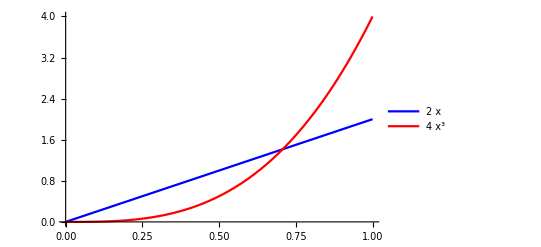

```mathematica
Plot[{2x,4x^3},{x,0,1},PlotStyle->{Blue,Red},PlotLegends->"Expressions"]
```

```mathematica
pdtable
```

{{t,dxy,dyz,dzx,dx2,dz2},{px,(1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,(1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ,l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ,-√3 l n^2 V_pdπ+l (1/2 (-l^2-m^2)+n^2) V_pdσ},{py,l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ,(1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ,-√3 m n^2 V_pdπ+m (1/2 (-l^2-m^2)+n^2) V_pdσ},{pz,-2 l m n V_pdπ+√3 l m n V_pdσ,m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ,l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ,-(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ,√3 (l^2+m^2) n V_pdπ+n (1/2 (-l^2-m^2)+n^2) V_pdσ}}

```mathematica
pdtableleft
```

{{t,dxy,dyz,dzx,dx2,dz2},{px,0,0,0,-1/2 √3 V_pdσ,V_pdσ/2},{py,-V_pdπ,0,0,0,0},{pz,0,0,-V_pdπ,0,0}}

```mathematica
(****** Three orbitals model (dxy, dx2,dz2)********)
```

```mathematica
lefthop=pdtableleft[[2;;4,2;;6]]
```

{{0,0,0,-1/2 √3 V_pdσ,V_pdσ/2},{-V_pdπ,0,0,0,0},{0,0,-V_pdπ,0,0}}

```mathematica
TableForm[lefthop]
```

0 | 0 | 0 | -1/2 √3 V_pdσ | V_pdσ/2
-V_pdπ | 0 | 0 | 0 | 0
0 | 0 | -V_pdπ | 0 | 0

```mathematica
righthop=pdtable[[2;;4,2;;6]]
```

{{(1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,(1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ,l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ,-√3 l n^2 V_pdπ+l (1/2 (-l^2-m^2)+n^2) V_pdσ},{l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ,(1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ,-2 l m n V_pdπ+√3 l m n V_pdσ,-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ,-√3 m n^2 V_pdπ+m (1/2 (-l^2-m^2)+n^2) V_pdσ},{-2 l m n V_pdπ+√3 l m n V_pdσ,m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ,l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ,-(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ,√3 (l^2+m^2) n V_pdπ+n (1/2 (-l^2-m^2)+n^2) V_pdσ}}

```mathematica
TableForm[righthop]
```

(1-2 l^2) m V_pdπ+√3 l^2 m V_pdσ | -2 l m n V_pdπ+√3 l m n V_pdσ | (1-2 l^2) n V_pdπ+√3 l^2 n V_pdσ | l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ | -√3 l n^2 V_pdπ+l (1/2 (-l^2-m^2)+n^2) V_pdσ
l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ | (1-2 m^2) n V_pdπ+√3 m^2 n V_pdσ | -2 l m n V_pdπ+√3 l m n V_pdσ | -m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ | -√3 m n^2 V_pdπ+m (1/2 (-l^2-m^2)+n^2) V_pdσ
-2 l m n V_pdπ+√3 l m n V_pdσ | m (1-2 n^2) V_pdπ+√3 m n^2 V_pdσ | l (1-2 n^2) V_pdπ+√3 l n^2 V_pdσ | -(l^2-m^2) n V_pdπ+1/2 √3 (l^2-m^2) n V_pdσ | √3 (l^2+m^2) n V_pdπ+n (1/2 (-l^2-m^2)+n^2) V_pdσ

```mathematica
(** diagonal terms **)
```

```mathematica
pp=1
dxypxdxy=lefthop[[pp,1]]righthop[[pp,1]]
dx2pxdx2=lefthop[[pp,4]]righthop[[pp,4]]
dz2pxdz2=lefthop[[pp,5]]righthop[[pp,5]]
```

1

0

-1/2 √3 V_pdσ (l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ)

1/2 V_pdσ (-√3 l n^2 V_pdπ+l (1/2 (-l^2-m^2)+n^2) V_pdσ)

```mathematica
pp=2
dxypydxy=lefthop[[pp,1]]righthop[[pp,1]]
dx2pydx2=lefthop[[pp,4]]righthop[[pp,4]]
dz2pydz2=lefthop[[pp,5]]righthop[[pp,5]]
```

2

-V_pdπ (l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ)

0

0

```mathematica
pp=3
dxypzdxy=lefthop[[pp,1]]righthop[[pp,1]]
dx2pzdx2=lefthop[[pp,4]]righthop[[pp,4]]
dz2pzdz2=lefthop[[pp,5]]righthop[[pp,5]]
```

3

0

0

0

```mathematica
(** off-diagonal terms **)
```

```mathematica
pp=1
dxypxdx2=lefthop[[pp,1]]righthop[[pp,4]]
dxypxdz2=lefthop[[pp,1]]righthop[[pp,5]]
```

1

0

0

```mathematica
pp=2
dxypydx2=lefthop[[pp,1]]righthop[[pp,4]]
dxypydz2=lefthop[[pp,1]]righthop[[pp,5]]
```

2

-V_pdπ (-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ)

-V_pdπ (-√3 m n^2 V_pdπ+m (1/2 (-l^2-m^2)+n^2) V_pdσ)

```mathematica
pp=3
dxypzdx2=lefthop[[pp,1]]righthop[[pp,4]]
dxypzdz2=lefthop[[pp,1]]righthop[[pp,5]]
```

3

0

0

```mathematica
pp=1
dx2pxdz2=lefthop[[pp,4]]righthop[[pp,5]]
```

1

-1/2 √3 V_pdσ (-√3 l n^2 V_pdπ+l (1/2 (-l^2-m^2)+n^2) V_pdσ)

```mathematica
pp=2
dx2pydz2=lefthop[[pp,4]]righthop[[pp,5]]
```

2

0

```mathematica
pp=3
dx2pzdz2=lefthop[[pp,4]]righthop[[pp,5]]
```

3

0

```mathematica
(*****we label dx2,dz2,dxy as 1,2,3 ****)
```

```mathematica
t11=dx2pxdx2+dx2pydx2+dx2pzdx2
t22=dz2pxdz2+dz2pydz2+dz2pzdz2
t33=dxypxdxy+dxypydxy+dxypzdxy
```

-1/2 √3 V_pdσ (l (1-l^2+m^2) V_pdπ+1/2 √3 l (l^2-m^2) V_pdσ)

1/2 V_pdσ (-√3 l n^2 V_pdπ+l (1/2 (-l^2-m^2)+n^2) V_pdσ)

-V_pdπ (l (1-2 m^2) V_pdπ+√3 l m^2 V_pdσ)

```mathematica
t23=dxypxdz2+dxypydz2+dxypzdz2
t23a=dxypxdx2+dxypydx2+dxypzdx2
```

-V_pdπ (-√3 m n^2 V_pdπ+m (1/2 (-l^2-m^2)+n^2) V_pdσ)

-V_pdπ (-m (1+l^2-m^2) V_pdπ+1/2 √3 m (l^2-m^2) V_pdσ)

```mathematica
td4={l->Cos[θ],m->Sin[θ],n->0}
```

{l→Cos[θ],m→Sin[θ],n→0}

```mathematica
beta=t23/t22/.td4/.pds->10pdpi(****)
betaa=t23a/t22/.td4/.pds->10pdpi(*****)
```

-Tan[θ]/5

-(Sec[θ] (5 √3 V_pdπ Sin[θ] (Cos[θ]^2-Sin[θ]^2)-V_pdπ Sin[θ] (1+Cos[θ]^2-Sin[θ]^2)))/(25 V_pdπ (-Cos[θ]^2-Sin[θ]^2))

```mathematica
ticks={0,Pi/6,Pi/3,π/2}
```

{0,π/6,π/3,π/2}

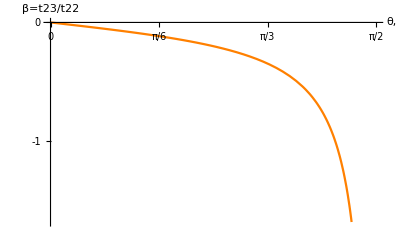

```mathematica
Plot[beta,{θ,0,π/2},Ticks->{ticks,{-3,-2,-1,0}},AxesLabel->{"θ,","β=t23/t22"},PlotStyle->Orange]
```

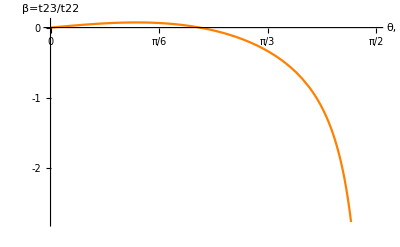

```mathematica
Plot[betaa,{θ,0,π/2},Ticks->{ticks,{-3,-2,-1,0}},AxesLabel->{"θ,","β=t23/t22"},PlotStyle->Orange]
```

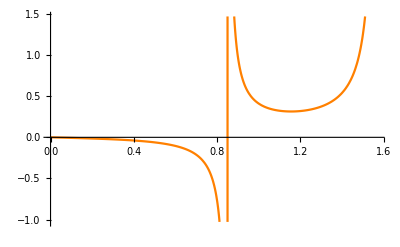

```mathematica
Plot[t23/t11/.td4//.pds->10pdpi//FullSimplify,{θ,0,π/2},PlotStyle->Orange]
```